```mathematica
eesticovid={{DateObject["2020-02-27"],1},{DateObject["2020-02-28"],1},{DateObject["2020-02-29"],1},{DateObject["2020-03-01"],1},{DateObject["2020-03-02"],2},{DateObject["2020-03-03"],3},{DateObject["2020-03-04"],3},{DateObject["2020-03-05"],5},{DateObject["2020-03-06"],10},{DateObject["2020-03-07"],10},{DateObject["2020-03-08"],10},{DateObject["2020-03-09"],10},{DateObject["2020-03-10"],13},{DateObject["2020-03-11"],17},{DateObject["2020-03-12"],41},{DateObject["2020-03-13"],79},{DateObject["2020-03-14"],115}, {DateObject["2020-03-15"],171}, {DateObject["2020-03-16"],205}, {DateObject["2020-03-17"],225}, {DateObject["2020-03-18"],258}}
```

{{Day: Thu 27 Feb 2020,1},{Day: Fri 28 Feb 2020,1},{Day: Sat 29 Feb 2020,1},{Day: Sun 1 Mar 2020,1},{Day: Mon 2 Mar 2020,2},{Day: Tue 3 Mar 2020,3},{Day: Wed 4 Mar 2020,3},{Day: Thu 5 Mar 2020,5},{Day: Fri 6 Mar 2020,10},{Day: Sat 7 Mar 2020,10},{Day: Sun 8 Mar 2020,10},{Day: Mon 9 Mar 2020,10},{Day: Tue 10 Mar 2020,13},{Day: Wed 11 Mar 2020,17},{Day: Thu 12 Mar 2020,41},{Day: Fri 13 Mar 2020,79},{Day: Sat 14 Mar 2020,115},{Day: Sun 15 Mar 2020,171},{Day: Mon 16 Mar 2020,205},{Day: Tue 17 Mar 2020,225},{Day: Wed 18 Mar 2020,258}}

```mathematica
eet = eesticovid//Transpose
```

{{Day: Thu 27 Feb 2020,Day: Fri 28 Feb 2020,Day: Sat 29 Feb 2020,Day: Sun 1 Mar 2020,Day: Mon 2 Mar 2020,Day: Tue 3 Mar 2020,Day: Wed 4 Mar 2020,Day: Thu 5 Mar 2020,Day: Fri 6 Mar 2020,Day: Sat 7 Mar 2020,Day: Sun 8 Mar 2020,Day: Mon 9 Mar 2020,Day: Tue 10 Mar 2020,Day: Wed 11 Mar 2020,Day: Thu 12 Mar 2020,Day: Fri 13 Mar 2020,Day: Sat 14 Mar 2020,Day: Sun 15 Mar 2020,Day: Mon 16 Mar 2020,Day: Tue 17 Mar 2020,Day: Wed 18 Mar 2020},{1,1,1,1,2,3,3,5,10,10,10,10,13,17,41,79,115,171,205,225,258}}

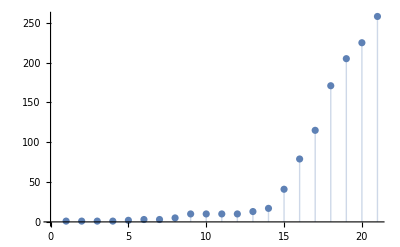

```mathematica
ListPlot[eet[[2]], Filling->Bottom]
```

```mathematica
Gompertz[b_,c_,x_]:=Exp[-b Ext[-c x]]
```

```mathematica
nlm = NonlinearModelFit[eet[[2]],Gompertz[b,c,x],{b,c},x]
```

NonlinearModelFit::nrlnum: The function value {-1.+Gompertz[1.,1.,1.],-1.+Gompertz[1.,1.,2.],-1.+Gompertz[1.,1.,3.],-1.+Gompertz[1.,1.,4.],-2.+Gompertz[1.,1.,5.],«11»,-115.+Gompertz[1.,1.,17.],-171.+Gompertz[1.,1.,18.],-205.+Gompertz[1.,1.,19.],-225.+Gompertz[1.,1.,20.],-258.+Gompertz[1.,1.,21.]} is not a list of real numbers with dimensions {21} at {b,c} = {1.,1.}.

NonlinearModelFit[{1,1,1,1,2,3,3,5,10,10,10,10,13,17,41,79,115,171,205,225,258},Gompertz[b,c,x],{b,c},x]